```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* constantes físicas *)
Clear[hbar,e,massae,eps0]
hbar=1.0545718 10^-34;(* constante de Planck *)
e=1.6021766 10^-19 ;(* carga do eletron *)
massae=9.10938356 10^-31 ;(* masa do eletron *)
eps0=8.8541878176 10^-12;(* constante de permissividade do vácuo *)
```

```mathematica
Clear[deltaEc,deltaEv,me,mh,ctedielet,camadas,a]
(* os seguintes dados são para nanocristais de Perovskita *)
deltaEc=1.25e; (* altura do poco do eletron *)
deltaEv=1.45e; (* altura do poco do buraco *)
me=massae.15 ;(* massa efetiva do eletron *)
mh=massae.14 ;(* massa efetiva do buraco *)
ctedielet=4.96; (* cte dieletrica *)
camadas=9; (* numero de camadas *)
a=camadas.59 10^-9/2;(* raio do nanorod *)
Print[2a]
```

5.31×10^-9

```mathematica
Clear[mi,eps]
(* outras constântes *)
mi=1/(1/me+1/mh); (* mu_perp *)
eps=ctedielet eps0; (* permissividade do material *)
```

```mathematica
Clear[keFunc,kappaeFunc,fTranscEFunc,EchuteE,khFunc,kappahFunc,fTranscHFunc,EchuteH]
keFunc[energia_]:=Sqrt[2me energia]/hbar(* função k do elétron *)
kappaeFunc[energia_]:=Sqrt[2me(deltaEc-energia)]/hbar(* função kappa do elétron *)
fTranscEFunc[energia_]:=keFunc[energia](BesselJ[-1,keFunc[energia]a]-BesselJ[1,keFunc[energia]a])+kappaeFunc[energia]BesselJ[0,keFunc[energia]a]/BesselK[0,kappaeFunc[energia]a](BesselK[-1,kappaeFunc[energia]a]+BesselK[1,kappaeFunc[energia]a])(* eq. transcendental do elétron *)
EchuteE[]:=(For[Ei=0,Ei<deltaEc,Ei+=deltaEc/1000,
If[fTranscEFunc[Ei]fTranscEFunc[Ei+deltaEc/1000 ]<0,Break[]]
];
Return[Ei])(* retorna um valor aproximado para o valor de energia correspondente a primeira raiz de fTranscEFunc *)
khFunc[energia_]:=Sqrt[2mh energia]/hbar(* função k do buraco *)
kappahFunc[energia_]:=Sqrt[2mh(deltaEv-energia)]/hbar(* função kappa do buraco *)
fTranscHFunc[energia_]:=khFunc[energia](BesselJ[-1,khFunc[energia]a]-BesselJ[1,khFunc[energia]a])+kappahFunc[energia]BesselJ[0,khFunc[energia]a]/BesselK[0,kappahFunc[energia]a](BesselK[-1,kappahFunc[energia]a]+BesselK[1,kappahFunc[energia]a])(* eq. transcendental do buraco *)
EchuteH[]:=(For[Ei=0,Ei<deltaEv,Ei+=deltaEv/1000,
If[fTranscHFunc[Ei]fTranscHFunc[Ei+deltaEv/1000 ]<0,Break[]]
];
Return[Ei])(* retorna um valor aproximado para o valor de energia correspondente a primeira raiz de fTranscHFunc *)
```

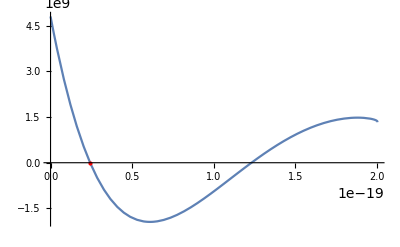

```mathematica
Clear[Ee,ke,kappae]
Ee=energia/.FindRoot[fTranscEFunc[energia],{energia,EchuteE[]}];
ke=keFunc[Ee];
kappae=kappaeFunc[Ee];
Show[Plot[fTranscEFunc[energia],{energia,0,deltaEc}],Graphics[{PointSize[Medium],Red,Point[{Ee,0}]}]]
```

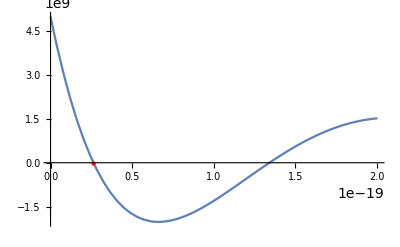

```mathematica
Clear[Eh,kh,kappah]
Eh=energia/.FindRoot[fTranscHFunc[energia],{energia,EchuteH[]}];
kh=khFunc[Eh];
kappah=kappahFunc[Eh];

Show[Plot[fTranscHFunc[energia],{energia,0,deltaEc}],Graphics[{PointSize[Medium],Red,Point[{Eh,0}]}]]
```

```mathematica
Clear[psieAux,psihAux]
(* função de onda analítica do elétron em função da distância x *)
psieAux[x_]:=Piecewise[{{BesselJ[0,ke x],0≤x<a},{BesselJ[0,ke a]/BesselK[0,kappae a]BesselK[0,kappae x],x≥a}}]
(* função de onda analítica do buraco em função da distância x *)
psihAux[x_]:=Piecewise[{{BesselJ[0,kh x],0≤x<a},{BesselJ[0,kh a]/BesselK[0,kappah a]BesselK[0,kappah x],x≥a}}]
```

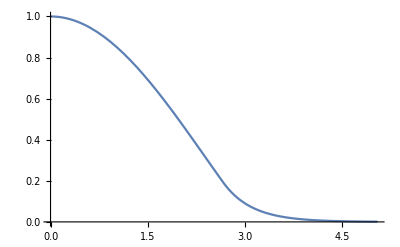

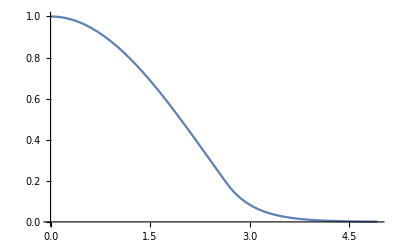

```mathematica
Clear[epsPsi,fTranscPsiE,fTranscPsiH]
(* vou considerar que as funções de onda são nulas para x ≥ L e para x ≤ L farei interpolação por motivos de otimização. 
O valor de L é tomado como sendo o ponto no qual a função de onda tem valor epsPsi *)
epsPsi=10^-3;
fTranscPsiE[x_]:=psieAux[x]-epsPsi
fTranscPsiH[x_]:=psihAux[x]-epsPsi
Le=x/.FindRoot[fTranscPsiE[x],{x,a}];(* L do elétron *)
Lh=x/.FindRoot[fTranscPsiH[x],{x,a}];(* L do buraco *)
(* interpolação da função de onda do elétron em função da distância x *)
psie=Interpolation[Table[{x,psieAux[x]},{x,0,Le,Le/100}]];
(* interpolação da função de onda do buraco em função da distância x *)
psih=Interpolation[Table[{x,psihAux[x]},{x,0,Lh,Lh/100}]];
Plot[psie[x],{x,0,Le}]
Plot[psih[x],{x,0,Lh}]
```

```mathematica
Clear[d,A,B,c,EsAux,Es,out,nome]
(* o ponto de mínimo é procurado em um range de lambda entre [lambIni, lambFin] com lambN pontos e um range de beta entre [betaIni, betaFin] com betaN pontos.
O método de integração usado é quase monte carlo, que tem um erro um pouco maior, porém é mais rápido.
Os integrandos foram calculados em um outro arquivo .nb utilizando a função D para calcular as derivadas de psir *)
lambIni=2. 10^-9;
lambFin=4. 10^-9;
lambN=5;
betaIni=.5;
betaFin=.98;
betaN=5;
Es={};(* array das energias calculadas para cada valor de beta e lamb *)
Timing[
For[beta=betaIni,beta≤betaFin,beta+=(betaFin-betaIni)/(betaN-1),
EsAux={};
For[lamb=lambIni,lamb≤lambFin,lamb+=(lambFin-lambIni)/(lambN-1),
d=NIntegrate[psie[rhoe]^2psih[rhoh]^2Exp[-2/lamb Sqrt[(1-beta^2)(rhoe^2+rhoh^2-2rhoe rhoh Cos[phi])+z^2]]rhoe rhoh,{rhoe,0,Le},{rhoh,0,Lh},{phi,0,2Pi},{z,0,10lamb}];
A=Ee d-hbar^2/2/me NIntegrate[psie[rhoe]^2psih[rhoh]^2
(1/lamb^2)(-1+beta^2) ⅇ^(-(2 √(z^2-(-1+beta^2) (rhoe^2+rhoh^2-2 rhoe rhoh Cos[phi])))/lamb) rhoh (-(((-1+beta^2) rhoe (rhoe-rhoh Cos[phi])^2)/(z^2-(-1+beta^2) (rhoe^2+rhoh^2-2 rhoe rhoh Cos[phi])))+(rhoh (-lamb ((-1+beta^2) rhoe^2+(-1+beta^2) rhoh^2-z^2) Cos[phi]+2 (-1+beta^2) lamb rhoe rhoh Cos[phi]^2+(-1+beta^2) rhoe rhoh (lamb+√(z^2-(-1+beta^2) (rhoe^2+rhoh^2-2 rhoe rhoh Cos[phi]))) Sin[phi]^2))/(z^2-(-1+beta^2) (rhoe^2+rhoh^2-2 rhoe rhoh Cos[phi]))^(3/2)),{rhoe,0,Le},{rhoh,0,Lh},{phi,0,2Pi},{z,0,7lamb},Method->"QuasiMonteCarlo"];
B=Eh d-hbar^2/2/mh NIntegrate[psie[rhoe]^2psih[rhoh]^2
(1/lamb^2)(-1+beta^2) ⅇ^(-(2 √(z^2-(-1+beta^2) (rhoe^2+rhoh^2-2 rhoe rhoh Cos[phi])))/lamb) rhoh (-(((-1+beta^2) rhoe (rhoe-rhoh Cos[phi])^2)/(z^2-(-1+beta^2) (rhoe^2+rhoh^2-2 rhoe rhoh Cos[phi])))+(rhoh (-lamb ((-1+beta^2) rhoe^2+(-1+beta^2) rhoh^2-z^2) Cos[phi]+2 (-1+beta^2) lamb rhoe rhoh Cos[phi]^2+(-1+beta^2) rhoe rhoh (lamb+√(z^2-(-1+beta^2) (rhoe^2+rhoh^2-2 rhoe rhoh Cos[phi]))) Sin[phi]^2))/(z^2-(-1+beta^2) (rhoe^2+rhoh^2-2 rhoe rhoh Cos[phi]))^(3/2)),{rhoe,0,Le},{rhoh,0,Lh},{phi,0,2Pi},{z,0,7lamb},Method->"QuasiMonteCarlo"];
c=-hbar^2/2/mi Re[NIntegrate[psie[rhoe]^2psih[rhoh]^2(ⅇ^(-(2 √(z^2-(-1+beta^2) (rhoe^2+rhoh^2-2 rhoe rhoh Cos[phi])))/lamb) rhoe rhoh ((-1+beta^2) lamb (rhoe^2+rhoh^2)-2 (-1+beta^2) lamb rhoe rhoh Cos[phi]+z^2 √(rhoe^2-beta^2 rhoe^2+rhoh^2-beta^2 rhoh^2+z^2+2 (-1+beta^2) rhoe rhoh Cos[phi])))/(lamb^2 (z^2-(-1+beta^2) (rhoe^2+rhoh^2-2 rhoe rhoh Cos[phi]))^(3/2)),{rhoe,0,Le},{rhoh,0,Lh},{phi,0,2Pi},{z,0,7lamb},Method->"QuasiMonteCarlo"]]
-e^2/4/Pi/eps NIntegrate[psie[rhoe]^2psih[rhoh]^2Exp[-2/lamb Sqrt[(1-beta^2)(rhoe^2+rhoh^2-2rhoe rhoh Cos[phi])+z^2]]/Sqrt[rhoe^2+rhoh^2-2rhoe rhoh Cos[phi]+z^2]rhoe rhoh,{rhoe,0,Le},{rhoh,0,Lh},{phi,0,2Pi},{z,0,7lamb},Method->"QuasiMonteCarlo"];
Eb=((A+B+c)/d-Ee-Eh)/e/10^-3;
AppendTo[EsAux,Eb]
];
AppendTo[Es,EsAux];
Print[EsAux]
]
][[1]]/60
valores={2a 10^9,lambIni 10^9,lambFin 10^9,lambN,betaIni,betaFin,betaN};
out={valores};
For[i=1,i≤betaN,i++,AppendTo[out,Es[[i]]]]
nome="nanorod_"<>ToString[2a 10^9]<>".csv";
Export[nome,out];(* exporta um arquivo .csv do array "valores" na primeira linha e o array "Es" nas demais linhas *)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.70667×10^-45 and 5.35637×10^-50 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained -4.16583×10^-28 and 5.75903×10^-29 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained -5.31951×10^-28 and 6.39293×10^-29 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.06754×10^-45 and 4.965×10^-50 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.60701×10^-45 and 5.33407×10^-50 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-88.561,-104.373,-109.905,-111.09,-110.283}

{-92.6547,-106.604,-111.241,-111.959,-110.895}

{-95.9047,-108.103,-111.984,-112.361,-111.146}

{-94.9908,-106.605,-110.548,-111.176,-110.242}

{-66.2054,-88.3554,-98.8771,-103.728,-105.572}

25.2224